## Física Moderna I - Rascunho

```mathematica
h =4.136*10^(-15);
c = 3*10^8;
Et=105*10^(3);

lambda0=(h*c)/Et
```

1.18171×10^-11

```mathematica
m0=9.11*10^(-31);
q=1.602*10^(-19);
COST=(m0*c^2)
CosT=COST/q
```

8.199×10^-14

511798.

```mathematica
N[(1/512-1/80+1/105)/(1/512)]
ArcCos[%]
```

-0.52381

2.12211

```mathematica
Rts^2
```

2.25×10^22

```mathematica
h =4.136*10^(-15);
c = 3*10^8;
lambda=0.1*10^(-10);
m0=9.11*10^(-31);
q=1.602*10^(-19);
p=h/lambda;
Ep=(h*c/lambda)
E0=(m0*c^2)/q
E1=Sqrt[(Ep)^2+(E0)^2]
K=E1-E0
nu=c/lambda
```

124080.

511798.

526624.

14826.2

3.×10^19

```mathematica
c = 3*10^8;
lambda=5890*10^(-10);
nu=N[c/lambda]
Deltanu=8*10^(6);
N[Deltanu/nu]
Deltat=10^(-8);
N[h/(4*Pi*Deltat)]
```

5.09338×10^14

1.57067×10^-8

3.29132×10^-8

```mathematica
h =4.136*10^(-15);
c = 3*10^8;
lambda=0.1*10^(-10);
m0=9.11*10^(-31);
```

1.53958×10^10

124080.

```mathematica
Solve[(L-x)^2==4*x^2,x]
Expand[(L-x)^2==4*x^2]
```

{{x→-L},{x→L/3}}

L^2-2 L x+x^2==4 x^2

## Física Moderna I - Relatividade

### Dilatação do tempo e Contração do espaço

```mathematica
Clear[γ,v]
c=3*10^8;
γ=1/Sqrt[1-v^2/c^2];
Plot[γ,{v, 0,c},GridLines->Automatic,PlotRange->{{0,c},{1,3}}]
Plot[Sqrt[1-v^2/c^2],{v, 0,c},GridLines->Automatic,PlotRange->{{0,c},{0,1}}]
```

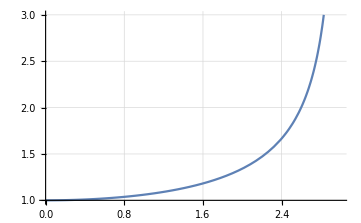
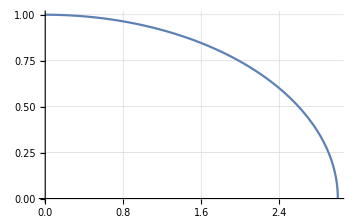

```mathematica
Clear[γ,v]
c=3*10^8; (* m/s *)
v=0.8*c; (* 80% da velocidade da Luz *)
γ=1/Sqrt[1-v^2/c^2]
DeltaTlinha = 10; (* segundos *)
DeltaT = γ*DeltaTlinha
L=100; (* metros *)
Llin=Sqrt[1-v^2/c^2]*L
```

1.51186

15.1186

66.1438

```mathematica
c=3*10^8;
v=0.85*c;
γ=1/Sqrt[1-v^2/c^2]
x=75;
t=2*10^(-5);
xl=γ*(x-v*t)
tl=γ*(t-x*v/c^2)
```

1.89832

-9539.04

```mathematica
xl=-9540;
tl=0.00003756;
x=γ*(xl+v*tl)
t=γ*(tl+v*xl/c^2)
```

71.7563

0.0000199893

```mathematica
ϕ=4.22;
h=4.136*10^(-15);
ν=ϕ/h
```

1.02031×10^15

```mathematica
c=3*10^8;
λ=560*10^(-9);
f=N[c/λ]
En1=h*f
En2=h*c/λ
```

5.35714×10^14

2.21571

2.21571

## Física Moderna I - Radiação Corpo Negro

```mathematica
Series[Exp[-x],{x,0,3}]
```

1-x+x^2/2-x^3/6+O[x]^4

```mathematica
Series[f[x],{x,a,3}]
```

f[a]+f'[a] (x-a)+1/2 f''[a] (x-a)^2+1/6 f^(3)[a] (x-a)^3+O[x-a]^4

```mathematica
Series[Exp[-x],{x,a,3}]
```

ⅇ^-a-ⅇ^-a (x-a)+1/2 ⅇ^-a (x-a)^2-1/6 ⅇ^-a (x-a)^3+O[x-a]^4

```mathematica
S1=Normal[%]
```

ⅇ^-a-ⅇ^-a (-a+x)+1/2 ⅇ^-a (-a+x)^2-1/6 ⅇ^-a (-a+x)^3

```mathematica
a=0;
S2=S1
```

1-x+x^2/2-x^3/6

```mathematica
Series[1/(1-x),{x,a,3}]
```

1+x+x^2+x^3+O[x]^4

## Física Moderna I - Principio de Incerteza

```mathematica
ω=2*Pi*(1);k=1;
fc[n_,t_]=Cos[(n+0.5)*Pi*k-ω*t];
Animate[Plot[fc[n,t],{n,0,3}],{t,0,2},AnimationRunning->False]
```

### Funções trigonométricas

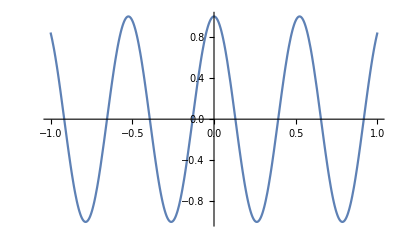

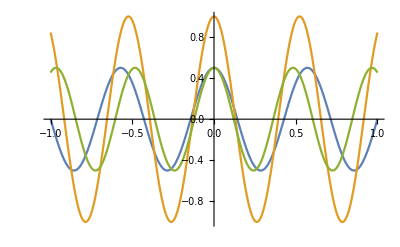

```mathematica
fk[k_,Ak_]=Ak*Cos[k*x];
xini=-12/12;
xfin=+12/12;
p1=Plot[fk[12,1],{x,xini,xfin}]
p2=Plot[{fk[11,1/2],fk[12,1],fk[13,1/2]},{x,xini,xfin}]
```

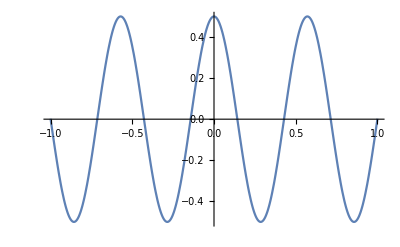

-Graphics-

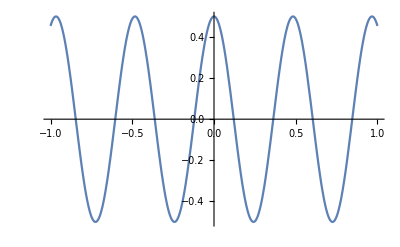

```mathematica
pk11=Plot[{fk[11,1/2]},{x,xini,xfin}]
pk12=Plot[{fk[12,1]},{x,xini,xfin}]
pk13=Plot[{fk[13,1/2]},{x,xini,xfin}]
```

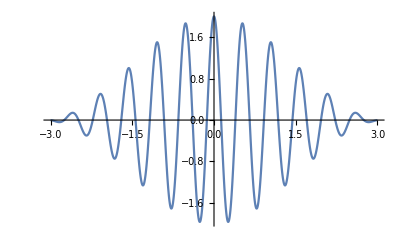

```mathematica
p3=Plot[{fk[11,1/2]+fk[12,1]+fk[13,1/2]},{x,3 xini,3 xfin}]
```

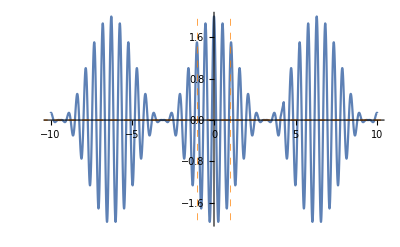

```mathematica
Plot[{fk[11,1/2]+fk[12,1]+fk[13,1/2]},{x,10 xini,10 xfin},GridLines->{{-1,1},{0,0}},GridLinesStyle->Directive[Orange,Dashed]]
```

1/4 Cos[9 x]+1/3 Cos[10 x]+1/2 Cos[11 x]+Cos[12 x]+1/2 Cos[13 x]+1/3 Cos[14 x]+1/4 Cos[15 x]

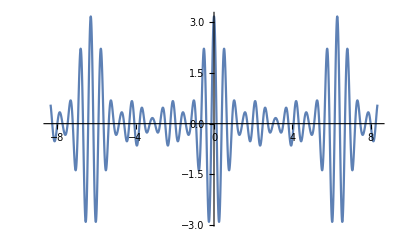

```mathematica
SumFk=fk[9,1/4]+fk[10,1/3]+fk[11,1/2]+fk[12,1]+fk[13,1/2]+fk[14,1/3]+fk[15,1/4]
xini=-100/12;
xfin=100/12;
p3=Plot[SumFk,{x,xini,xfin},PlotRange->All]
```

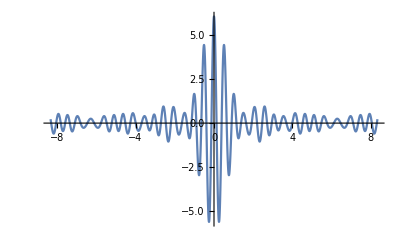

```mathematica
SumFk=fk[9,1/4]+fk[10,1/3]+fk[11,1/2]+fk[12,1]+fk[13,1/2]+fk[14,1/3]+fk[15,1/4]+fk[9.5,1/4]+fk[10.5,1/3]+fk[11.5,1/2]+fk[12.5,1]+fk[13.5,1/2]+fk[14.5,1/3];
xini=-100/12;
xfin=100/12;
p3=Plot[SumFk,{x,xini,xfin},PlotRange->All]
```

## Física Moderna II - Equação de Schrodinger (Cap-5)

### Funções trigonométricas

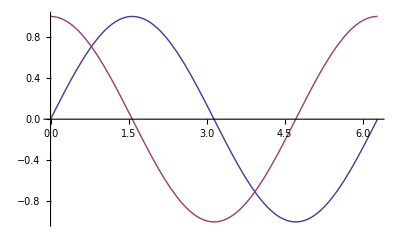

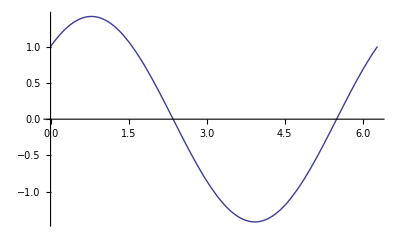

```mathematica
fs[θ_]=Sin[θ];
fc[θ_]=Cos[θ];
f2[θ_]=Sin[θ]+Cos[θ];
p1=Plot[{fs[θ],fc[θ]},{θ,0,2*Pi}]
p2=Plot[{fs[θ]+fc[θ]},{θ,0,2*Pi}]
```

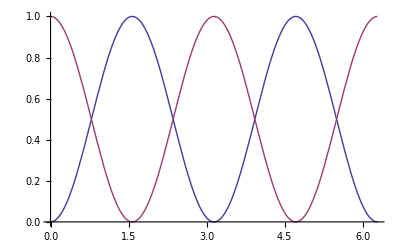

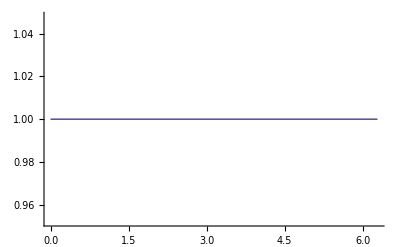

```mathematica
p3=Plot[{fs[θ]^2,fc[θ]^2},{θ,0,2*Pi}]
p4=Plot[{fs[θ]^2+fc[θ]^2},{θ,0,2*Pi}]
```

### Oscilador Harmônico Simples (OHS)

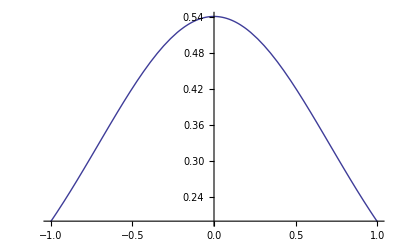

```mathematica
A=1;
c1=1;
c2=1;
fohs[x_]=A*Exp[-c1*x^2]*Exp[-I*c2];
p1=Plot[{Re[fohs[x]]},{x,-1,1}]
```

### Potencial Molécula diatômica (md)

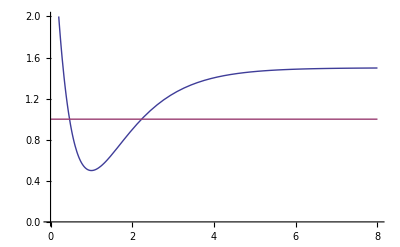

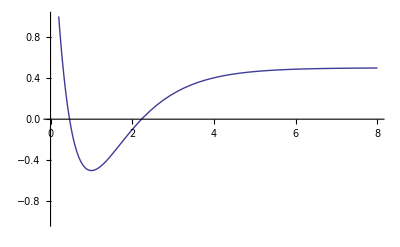

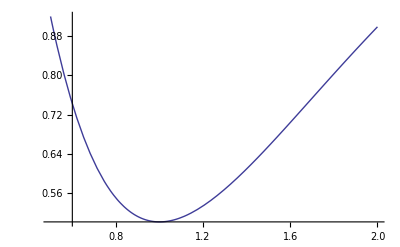

```mathematica
Vo=1;
re=1;
a=1;
VL[x_]=Vo*((re/x)^(12) - 2*(re/x)^6); (* V de Lennard-Jones *)
VM[x_]=Vo*((1-Exp[-a*(x-re)])^2-1)+1.5; (* V de Morse *)
Ex[x_]=1.0; (* Constante *)
p1=Plot[{VM[x],Ex[x]},{x,0,8},PlotRange-> {{0,8},{0,2}}]
p1=Plot[{VM[x]-Ex[x]},{x,0,8},PlotRange-> {{0,8},{-1,1}}]
p2=Plot[{VM[x]},{x,0.5,2}]
```

### Funções trigonométricas

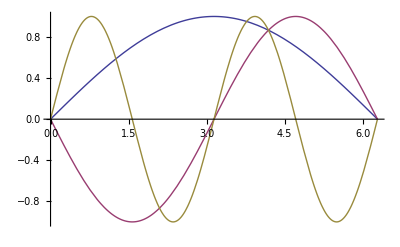

```mathematica
fs1[θ_]=Sin[0.5*θ];
fs2[θ_]=-Sin[1*θ];
fs3[θ_]=Sin[2*θ];
p1=Plot[{fs1[θ],fs2[θ],fs3[θ]},{θ,0,2*Pi}]
```

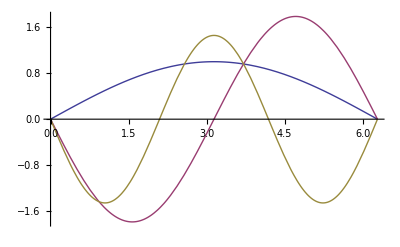

0.960025

0.960419

0.960379

```mathematica
fs1[θ_]=(1.0)*Sin[0.5*θ];
fs2[θ_]=-(1.787)*Sin[1*θ];
fs3[θ_]=-(1.457)*Sin[1.5*θ];
p1=Plot[{fs1[θ],fs2[θ],fs3[θ]},{θ,0,2*Pi}]
θo=3.709;
fs1[θo]
fs2[θo]
fs3[θo]
```

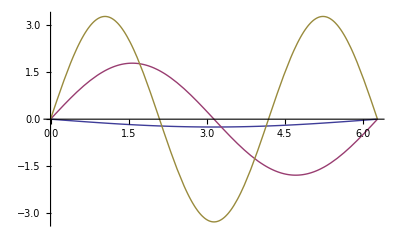

```mathematica
li=0;
lf=2*Pi;
dxs1=D[fs1[θ],θ];
dxs2=D[fs2[θ],θ];
dxs3=D[fs3[θ],θ];
p2=Plot[{dxs1,dxs2,dxs3},{θ,li,lf}];
d2xs1=D[D[fs1[θ],θ],θ];
d2xs2=D[D[fs2[θ],θ],θ];
d2xs3=D[D[fs3[θ],θ],θ];
p2=Plot[{d2xs1,d2xs2,d2xs3},{θ,li,lf}]
```

### Plot comportamento da f.o.

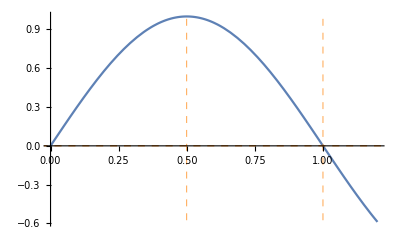

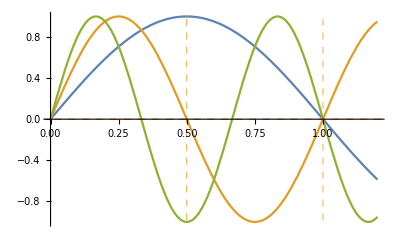

```mathematica
Clear[n]
A=1;
λ=1.0;
xm=1.2;
fs1[x_,n_]=A*Sin[(n*Pi/λ)*x];
p1=Plot[{fs1[x,1]},{x,0,xm},GridLines->{{0.5,1},{0,0}},GridLinesStyle->Directive[Orange,Dashed]]
p2=Plot[{fs1[x,1],fs1[x,2],fs1[x,3]},{x,0,xm},GridLines->{{0.5,1},{0,0}},GridLinesStyle->Directive[Orange,Dashed]]
p3=Plot[{fs1[x,1]^2,fs1[x,2]^2,fs1[x,3]^2},{x,0,xm}];
```

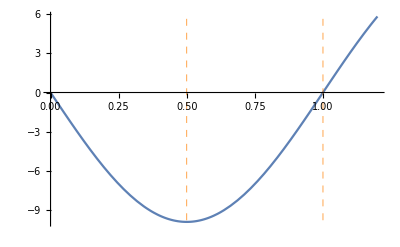

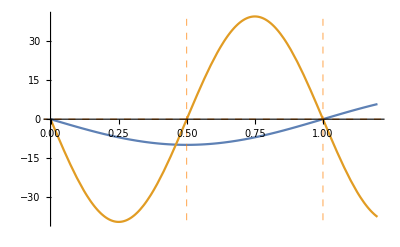

```mathematica
d2xs1=D[D[fs1[x,1],x],x];
d2xs2=D[D[fs1[x,2],x],x];
p4=Plot[{d2xs1},{x,0,xm},GridLines->{{0.5,1},{0,0}},GridLinesStyle->Directive[Orange,Dashed]]
p5=Plot[{d2xs1,d2xs2},{x,0,xm},GridLines->{{0.5,1},{0,0}},GridLinesStyle->Directive[Orange,Dashed]]
```

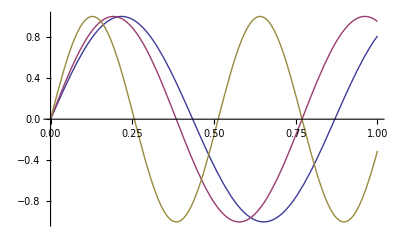

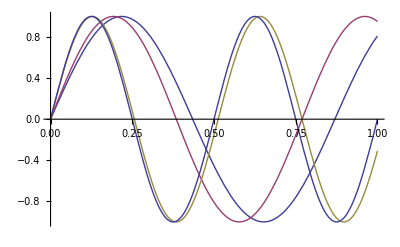

```mathematica
p1=Plot[{fs1[x,2.3],fs1[x,2.6],fs1[x,3.9]},{x,0,λ}]
p2=Plot[{fs1[x,4]},{x,0,λ}];
Show[p1,p2]
```

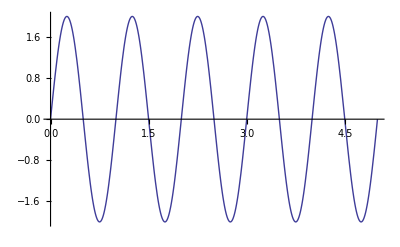

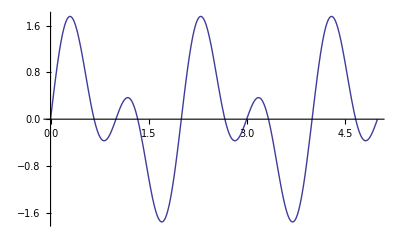

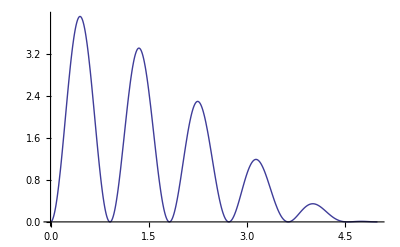

```mathematica
Clear[n]
A=1;
λ=1;
fs1[x_,n_]=A*Sin[(n*Pi/λ)*x];
fs2[x_,n_]=A*Sin[(n*Pi/λ)*x];
p1=Plot[{fs1[x,2]+fs2[x,2]},{x,0,5*λ}]
p2=Plot[{fs1[x,1]+fs2[x,2]},{x,0,5*λ}]
p3=Plot[{(fs1[x,1]+fs2[x,1.2])^2},{x,0,5*λ}]
```

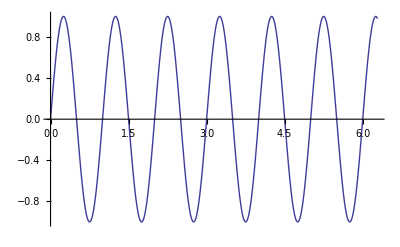

```mathematica
A=1;
ϕo=0;
λ=1;
fs1[x_]=A*Sin[(2*Pi/λ)*x+ϕo];
fs2[x_]=A*Sin[(2*Pi/λ)*x+ϕo];
fs3[x_]=A*Sin[(2*Pi/λ)*x+ϕo];
p1=Plot[{fs1[x]},{x,0,2*Pi}]
```

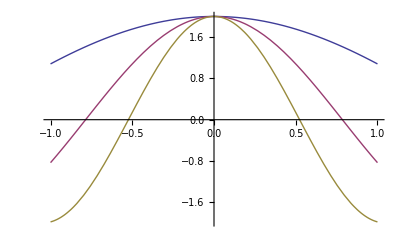

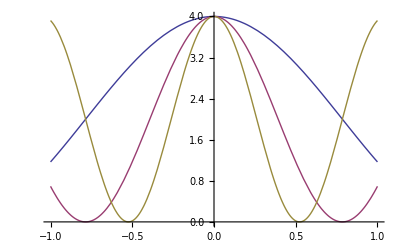

```mathematica
Clear[n]
A=1;
B=1;
λ=1;
fs[x_,k_]=A*Exp[I*k*x]+B*Exp[-I*k*x];
p1=Plot[{fs[x,1],fs[x,2],fs[x,3]},{x,-λ,λ}]
p2=Plot[{fs[x,1]^2,fs[x,2]^2,fs[x,3]^2},{x,-λ,λ}]
```

## Física Moderna II - Soluções da Equação de Schrodinger (Cap-6)

### Potencial Nulo (V=0)

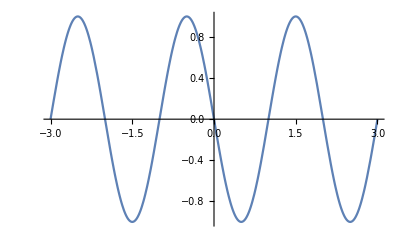

```mathematica
fe[n_]=Exp[I*(n+0.5)*Pi];
p1=Plot[{Re[fe[n]]},{n,-3,3}]
```

```mathematica
ω=2*Pi*(1);k=1;
fe[n_,t_]=Exp[I*(n+0.5)*Pi*k-ω*t];
fc[n_,t_]=Cos[(n+0.5)*Pi*k-ω*t];
Animate[Plot[fc[n,t],{n,0,3}],{t,0,2},AnimationRunning->False];
Animate[Plot[fc[n,t]^2,{n,0,3}],{t,0,2},AnimationRunning->False]
```

```mathematica
ω=2*Pi*(1);k=1;
fcp[n_,t_]=Cos[(n+0.5)*Pi*k-ω*t];
fcn[n_,t_]=Cos[-(n+0.5)*Pi*k-ω*t+Pi];
Animate[Show[Plot[fcn[n,t],{n,-3,0}],Plot[fcp[n,t],{n,0,3}],PlotRange-> {{-3,3},{-1,1}}],{t,0,5},AnimationRunning->False]
Animate[Plot[{fcn[n,t],fcp[n,t]},{n,-3,3}],{t,0,3},AnimationRunning->False];
Animate[{Plot[fcn[n,t],{n,-3,0}],Plot[fcp[n,t],{n,0,3}]},{t,0,5},AnimationRunning->False];
```

1

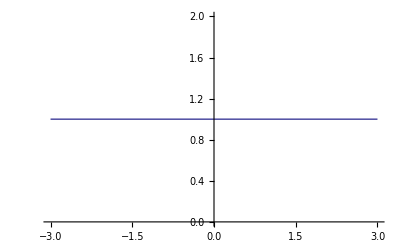

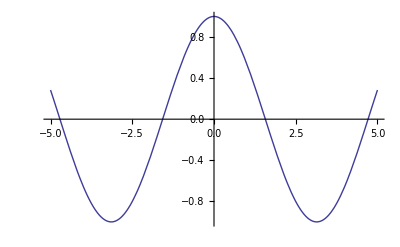

```mathematica
ψ[x_,t_]=Exp[I*(k*x-ω*t)];
ψs[x_,t_]=Exp[-I*(k*x-ω*t)];
DensProb=ψs[x,t]*ψ[x,t]
Plot[{DensProb},{n,-3,3}]
ω=2*Pi*(1);k=1;
Plot[{Re[ψ[x,1]]},{x,-5,5}]
```

```mathematica
r=1;step=0.1;
backgroundAxes=Plot[0,{x,-Pi,3*Pi},PlotRange->{Automatic,{-r/2,2*r+0.5}},AspectRatio->Automatic];

(* Animate[Show[{backgroundAxes,ListPlot[Table[{x-Sin[x],1-Cos[x]},{x,0,t,step}],Joined->True],Graphics[{PointSize[Large],Red,Point[{t-Sin[t],1-Cos[t]}]}],Graphics[Circle[{t,1},r]]}],{t,0,4*Pi,step},AnimationRate->5]
```

## testes

```mathematica
Integrate[Cos[2*Pi*x/a]^2,{x,-a/2,+a/2}]
Integrate[x*Sin[2*Pi*x/a]^2,{x,-a/2,+a/2}]
Integrate[x*Sin[2*Pi*x/a]^2,{x,-a/2,+a/2}]
Integrate[Sin[u]^2,{u,-Pi,+Pi}]
```

a/2

0

π

u/2-1/4 Sin[2 u]

```mathematica
I1=Integrate[x^2*Sin[2*Pi*x/a]^2,{x,-a/2,+a/2}]
I2=2*I1/a
```

(a^3 (-3+2 π^2))/(48 π^2)

(a^2 (-3+2 π^2))/(24 π^2)

```mathematica
Integrate[Sin[u],{u,0,Pi}]
Integrate[a,{u,0,+2 Pi}]
Integrate[u*Exp[-u],{u,0,Infinity}]
```

2

2 a π

1

```mathematica
N[(3*10^4)*(3*10^4)/(3*10^8)^2]
N[0.998^2]
λc=N[4.13*10^(-15)*3*10^8]
N[λc*10^9/400]-1.9
```

1.×10^-8

0.996004

1.239×10^-6

1.1975